FittedModel[2.81178+0.864777 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.81178 | 0.169467 | 16.592 | 2.16409×10^-28
x | 0.864777 | 0.000996102 | 868.161 | 1.42295×10^-169

{2.81178+0.864777 x-1.98827 √(0.0287189-0.000113044 x+9.92219×10^-7 x^2),2.81178+0.864777 x+1.98827 √(0.0287189-0.000113044 x+9.92219×10^-7 x^2)}

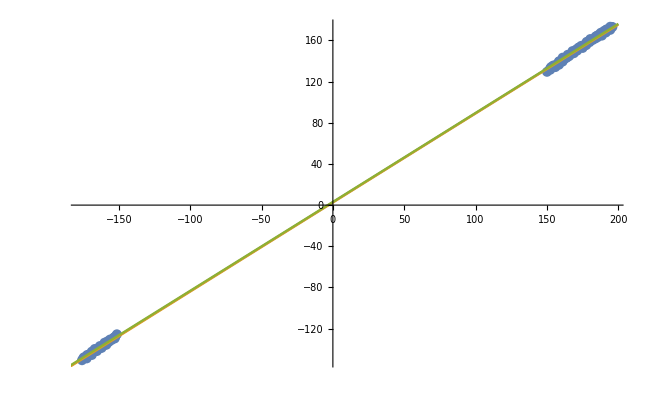

```mathematica
data = Import["~/mnt/phys3117/lab4/ALL0003-squid.tsv", "tsv"][[2;;All]];
data = Select[data, #[[1]] ≤ -150 || #[[1]] ≥ 150 &];
fit = LinearModelFit[data, x, x]
fit["ParameterTable"]
fit["MeanPredictionBands"]
Show[ListPlot[data, PlotRange -> All], Plot[Evaluate@{Normal[fit], fit["MeanPredictionBands"]}, {x, -200, 200}]]
```

FittedModel[Piecewise[{{3.12797+0.0308501 x, x<40.0847}, {-54.6806+1.47301 x, x≥40.0847}, {0, True}}]]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0308501 | 0.00568506 | 5.42652 | 2.68635×10^-7
b | 1.47301 | 0.0300261 | 49.0578 | 3.50471×10^-86
c | 3.12797 | 0.120065 | 26.0523 | 1.1628×10^-53
k | 40.0847 | 0.263628 | 152.05 | 3.3414×10^-149

{Piecewise[{{-54.6806+1.47301 x-1.97824 √(2.24255-0.08931 x+0.000901565 x^2), x≥40.0847}, {3.12797+0.0308501 x-1.97824 √(0.0144156-0.00082343 x+0.0000323199 x^2), True}}],Piecewise[{{-54.6806+1.47301 x+1.97824 √(2.24255-0.08931 x+0.000901565 x^2), x≥40.0847}, {3.12797+0.0308501 x+1.97824 √(0.0144156-0.00082343 x+0.0000323199 x^2), True}}]}

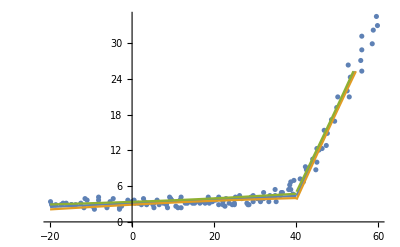

```mathematica
data = Import["~/mnt/phys3117/lab4/ALL0003-squid.tsv", "tsv"][[2;;All]];
data = Select[data, -20 ≤ #[[1]] ≤ 60 &];
fit = NonlinearModelFit[data, Piecewise[{{a x + c, x < k}, {b x + (a k + c - b k), x ≥ k}}], {a, b, c, k}, x]
fit["ParameterTable"]
fit["MeanPredictionBands"]
Show[ListPlot[data, PlotRange -> All], Plot[Evaluate@{Normal[fit], fit["MeanPredictionBands"]}, {x, -20, 60}]]
```

FittedModel[9.8048+3.22955 Cos[0.149254+0.0655617 x]]

| Estimate | Standard Error | t-Statistic | P-Value
a | 3.22955 | 0.0359515 | 89.8307 | 5.28494889494×10^-309
T | 95.8362 | 0.319447 | 300.007 | 6.10591239503×10^-563
ϕ | 0.149254 | 0.0112409 | 13.2778 | 1.21903×10^-34
c | 9.8048 | 0.0266003 | 368.597 | 4.2870557965×10^-607

{9.8048+3.22955 Cos[0.149254+0.0655617 x]-1.96476 √(0.000707577-0.000167262 Cos[0.149254+0.0655617 x]+0.00129251 Cos[0.149254+0.0655617 x]^2+(-0.0000500304+0.0000101996 x) Sin[0.149254+0.0655617 x]+(0.00131791+2.15923×10^-6 x+4.98105×10^-7 x^2) Sin[0.149254+0.0655617 x]^2+7.51459×10^-6 Sin[0.298509+0.131123 x]+6.5486×10^-7 x Sin[0.298509+0.131123 x]),9.8048+3.22955 Cos[0.149254+0.0655617 x]+1.96476 √(0.000707577-0.000167262 Cos[0.149254+0.0655617 x]+0.00129251 Cos[0.149254+0.0655617 x]^2+(-0.0000500304+0.0000101996 x) Sin[0.149254+0.0655617 x]+(0.00131791+2.15923×10^-6 x+4.98105×10^-7 x^2) Sin[0.149254+0.0655617 x]^2+7.51459×10^-6 Sin[0.298509+0.131123 x]+6.5486×10^-7 x Sin[0.298509+0.131123 x])}

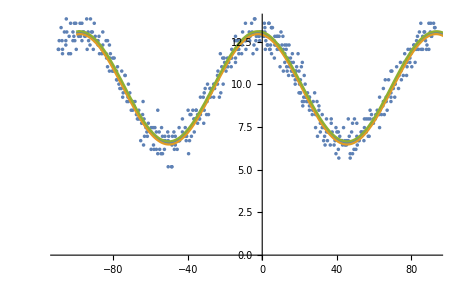

```mathematica
data = Import["~/mnt/phys3117/lab4/ALL0002-squid.tsv", "tsv"][[2;;All]];
fit = NonlinearModelFit[data,a Cos[2 π x/T + ϕ] + c, {a, {T, 100}, ϕ, c}, x]
fit["ParameterTable"]
fit["MeanPredictionBands"]
Show[ListPlot[data, PlotRange -> All], Plot[Evaluate@{Normal[fit], fit["MeanPredictionBands"]}, {x, -100, 100}]]
```

```mathematica
1.96 Sqrt@Length[data] fit["ParameterErrors"]
```

{1.57564,14.0004,0.492654,1.16581}

```mathematica
Reduce[Eliminate[{βL == 4 Ic RN/(π V)(1 - const Sqrt[kB T L]/Φ0) - 1, βL == 2 Ic L/Φ0}, βL], L]
Reduce[Eliminate[{βL == 4 Ic RN/(π V)(1 - const Sqrt[kB T L]/Φ0) - 1, βL == 2 Ic L/Φ0}, L], βL]
```

Ic V≠0&&(L==1/(2 Ic^2 π^2 V^2)(4 const^2 Ic^2 kB RN^2 T+4 Ic^2 π RN V Φ0-Ic π^2 V^2 Φ0-2 √2 √(2 const^4 Ic^4 kB^2 RN^4 T^2+4 const^2 Ic^4 kB π RN^3 T V Φ0-const^2 Ic^3 kB π^2 RN^2 T V^2 Φ0))||L==1/(2 Ic^2 π^2 V^2)(4 const^2 Ic^2 kB RN^2 T+4 Ic^2 π RN V Φ0-Ic π^2 V^2 Φ0+2 √2 √(2 const^4 Ic^4 kB^2 RN^4 T^2+4 const^2 Ic^4 kB π RN^3 T V Φ0-const^2 Ic^3 kB π^2 RN^2 T V^2 Φ0)))&&Φ0≠0

V Φ0≠0&&(βL==1/(π^2 V^2 Φ0)(4 const^2 Ic kB RN^2 T+4 Ic π RN V Φ0-π^2 V^2 Φ0-2 √2 √(2 const^4 Ic^2 kB^2 RN^4 T^2+4 const^2 Ic^2 kB π RN^3 T V Φ0-const^2 Ic kB π^2 RN^2 T V^2 Φ0))||βL==1/(π^2 V^2 Φ0)(4 const^2 Ic kB RN^2 T+4 Ic π RN V Φ0-π^2 V^2 Φ0+2 √2 √(2 const^4 Ic^2 kB^2 RN^4 T^2+4 const^2 Ic^2 kB π RN^3 T V Φ0-const^2 Ic kB π^2 RN^2 T V^2 Φ0)))

```mathematica
L = 1/(2 Ic^2 π^2 V^2)(4 const^2 Ic^2 kB RN^2 T+4 Ic^2 π RN V Φ0-Ic π^2 V^2 Φ0-2 √2 √(2 const^4 Ic^4 kB^2 RN^4 T^2+4 const^2 Ic^4 kB π RN^3 T V Φ0-const^2 Ic^3 kB π^2 RN^2 T V^2 Φ0));
βL = 1/(π^2 V^2 Φ0)(4 const^2 Ic kB RN^2 T+4 Ic π RN V Φ0-π^2 V^2 Φ0-2 √2 √(2 const^4 Ic^2 kB^2 RN^4 T^2+4 const^2 Ic^2 kB π RN^3 T V Φ0-const^2 Ic kB π^2 RN^2 T V^2 Φ0));
{
{βL, Norm[Grad[βL, {Ic, RN, V}]{DIc, DRN, DV}]},
UnitConvert[{L, Norm[Grad[L, {Ic, RN, V}]{DIc, DRN, DV}]}, "Picohenries"]
} /. {
const -> 3.57,
kB -> Quantity["BoltzmannConstant"],
T -> Quantity[77.355, "Kelvins"],
Φ0 -> Quantity["PlanckConstant"]/(2 Quantity["ElementaryCharge"]),
Ic -> Quantity[40.084679639219225/2, "Microamperes"],
DIc -> Quantity[6.0036363266340675/2, "Microamperes"],
RN -> Quantity[2 0.8647766685706172,"Volts"/"Amperes"],
DRN -> Quantity[2 0.01821040266880522,"Volts"/"Amperes"],
V -> Quantity[2 3.2295459157479893,"Microvolts"],
DV -> Quantity[2 1.5756432620326004,"Microvolts"]
}
```

Thread::tdlen: Objects of unequal length in {2, const, Ic, kB, RN, T} + {4, const, Ic, kB, π, RN, T, V, Φ0} + {-1, const, Ic, kB, π, RN, T, V, Φ0} cannot be combined.

Thread::tdlen: Objects of unequal length in {4, const, Ic, kB, RN, T} + {4, Ic, π, RN, V, Φ0} + {-1, Ic, π, V, Φ0} + {-2, 2, {2, const, Ic, kB, RN, T} + {-1, const, Ic, kB, π, RN, T, V, Φ0} + {4, const, Ic, kB, π, RN, T, V, Φ0}} cannot be combined.

Thread::tdlen: Objects of unequal length in {8, const, Ic, kB, RN, T} + {12, const, Ic, kB, π, RN, T, V, Φ0} + {-2, const, Ic, kB, π, RN, T, V, Φ0} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

{{1.95824,0.814352},{101.019 pH,37.6613 pH}}